# Shape 2: an ellipsoid with an offset centre of mass

## Does moving the CoM off the centre of force, in any direction, give the chirality needed for orbits?

The body is the near-spherical ellipsoid of Shape 1, now with a small linear density gradient that moves the centre of mass (CoM) off the geometric centre H. Since the ellipsoid is centrosymmetric, H is also its centre of force. As before, the gradient is uniform, ∇ln T = -G Ẑ, with no trap. The response (F, τ) = -ℛ·(∇ln T, v, ω) is taken about the CoM.

Results in brief. (1) An offset along a principal axis gives symmetry C_(2v), and an offset in a principal plane gives C_s. On a triaxial ellipsoid an offset in a generic direction leaves no symmetry at all (C_1), so the particle is chiral. (2) All four tensors follow exactly from those of Shape 1 by a rigid shift. In particular T_th = -[r_c]_×f_th. (3) This chirality is invisible to the gas. T_drag^-1 T_th never has a real non-zero eigenvalue, whatever the offset direction. The reason: at levitation the net gas force is vertical and acts through H, so it has no moment about the vertical. (4) The particle hangs with its CoM below H, as a damped pendulum, and then glides in a straight line (offset in a mirror plane or generic) or hovers (offset along an axis). (5) There is no orbit for any offset: R = ∞ and there is no period.

## 1. Setup

```mathematica
ClearAll["Global`*"];
shapesDir=Quiet@Check[NotebookDirectory[],$Failed];If[!StringQ[shapesDir],shapesDir=Environment["SHAPES_DIR"]];
Get[FileNameJoin[{shapesDir,"ShapeLevitation.wl"}]];
$verifications={};
record[ref_,claim_,status_,detail_]:=(AppendTo[$verifications,{ref,claim,status,detail}];VR[ref,claim,status,detail]);
VR/:MakeBoxes[VR[ref_,claim_,status_,detail_],fmt_]:=ToBoxes[Panel[Column[{Row[{Style[status,Bold,If[status=="VERIFIED",Darker[Green],Red]],"   ",Style[ref,Bold],":  ",claim}],If[detail==="",Nothing,detail]}]],fmt];
check[ref_String,claim_String,test_,detail_:""]:=record[ref,claim,If[TrueQ[test],"VERIFIED","DISCREPANCY"],detail];
zeroQ[expr_]:=AllTrue[Flatten[{Simplify[expr]}],PossibleZeroQ];
sci[x_]:=If[x==0,"0",Module[{e=Floor[Log10[Abs[N[x]]]]},ToString[NumberForm[N[x]/10^e,{3,2}]]<>"e"<>ToString[e]]];
num[x_,d_:4]:=If[x!=0&&(Abs[x]<10^-3||Abs[x]>=10^5),sci[x],ToString[NumberForm[N[x],d]]];
vec[v_,d_:3]:="("<>StringRiffle[num[#,d]&/@v,", "]<>")";
tf[m_]:=TraditionalForm[MatrixForm[m]];
n={x,y,z};
gas=gasModel[];ell=20*^-6;rhoP=1000.;
```

## 2. The shape and the mass distribution

The surface is the ellipsoid of Shape 1, with semi-axes a_i = 1 + ε e_i (units of l), defaults ε = 0.1 and e = (1, 0, -1). The density is ρ_p(1 + κ d̂·r/l), with unit direction d̂ and strength κ. Because ∮ r_i r_j dV = V/5 a_i^2 l^2 δ_ij for an ellipsoid, the CoM sits at

r_c = κl/5 diag(a_1^2, a_2^2, a_3^2) d̂    (exact;  |r_c| ≈ 0.1l = 2 μm for κ = 0.5)

```mathematica
a1=1+epse1;a2=1+epse2;a3=1+epse3;
Rellipsoid[{x_,y_,z_}]:=1/Sqrt[x^2/a1^2+y^2/a2^2+z^2/a3^2];
density[r_,dhat_,kappa_]:=1+kappadhat.r;
defaults={eps->1/10,e1->1,e2->0,e3->-1};kappa0=0.5;
Rnum[nn_List]:=Rellipsoid[nn]/.defaults;
offsets=<|"along x (C2v)"->{1,0,0},"in the x-z plane (Cs)"->Normalize[{1,0,1}],"generic (C1, chiral)"->Normalize[{1,2,3}]|>;
Row[{"R(n) = ",TraditionalForm[Rellipsoid[n]],",   rho/rho_p = ",TraditionalForm[density[{X,Y,Z},{d1,d2,d3},kappa]],",   defaults ",defaults,", kappa = ",kappa0}]
```

R(n) = 1/(√(x^2/(e1 eps+1)^2+y^2/(e2 eps+1)^2+z^2/(e3 eps+1)^2)),   rho/rho_p = kappa (d1 X+d2 Y+d3 Z)+1,   defaults {eps→1/10,e1→1,e2→0,e3→-1}, kappa = 0.5

Three offset directions represent the three symmetry classes that an offset can produce on a triaxial ellipsoid:

offset direction d̂ | symmetry of body + mass | surviving elements | chiral?
along a principal axis, e.g. x̂ | C_(2v) | the two-fold axis along d̂ and two mirror planes containing it | no
in a principal plane, e.g. (x̂ + ẑ)/√2 | C_s | the mirror plane containing d̂ | no
generic, e.g. (1, 2, 3)/√14 | C_1 | none | **yes**

(For a spheroid, a_1 = a_2, even a generic offset leaves the mirror plane that contains the symmetry axis and d̂. So only a triaxial ellipsoid can be made chiral this way.) Next, build the three particles by numerical quadrature, and check the CoM formula and convexity.

```mathematica
pts=Association[KeyValueMap[#1->makeParticle[Rnum,ell,rhoP,gas,Function[r,density[r,#2,kappa0]]]&,offsets]];
pt0=makeParticle[Rnum,ell,rhoP,gas];
rcExact[dhat_]:=kappa0ell/5DiagonalMatrix[N[{a1,a2,a3}^2/.defaults]].dhat;
Column[Join[{check["convex","the surface (Shape 1) is convex",convexityMargin[Rnum]>0]},KeyValueMap[check["CoM "<>#1,"CoM = (kappa l/5) diag(a_i^2).d",Norm[#2["com"]-rcExact[offsets[#1]]]<10^-9ell,"r_c/l = "<>vec[#2["com"]/ell,4]]&,pts]]]
```

✓ VERIFIED    convex:   the surface (Shape 1) is convex

✓ VERIFIED    CoM along x (C2v):   CoM = (κ l/5) diag(a_i^2).d
r_c/l = (0.121, -8.46e-20, -2.97e-17)

✓ VERIFIED    CoM in the x-z plane (Cs):   CoM = (κ l/5) diag(a_i^2).d
r_c/l = (0.08556, -2.21e-18, 0.05728)

✓ VERIFIED    CoM generic (C1, chiral):   CoM = (κ l/5) diag(a_i^2).d
r_c/l = (0.03234, 0.05345, 0.06494)

## 3. Diagram

Each panel shows the body coloured by R - 1 (red is long), the geometric centre H (black) and the CoM (magenta). The magenta arrow is r_c drawn 5 times longer than scale. In the chiral case the arrow leans out of every principal plane.

```mathematica
Row[KeyValueMap[Show[shapeDiagram[Rnum,5#2["com"]/ell,PlotLabel->#1,ImageSize->205],Graphics3D[{Magenta,Arrow[Tube[{{0,0,0},5#2["com"]/ell},0.03]]}]]&,pts]]
```

-Graphics3D--Graphics3D--Graphics3D-

## 4. The four tensors

The gas sees only the surface. Every stress therefore acts exactly as in Shape 1, about H, where T_th^H = B^H = 0. Moving the reference point from H to the CoM changes the lever arm, r_H = -r_c, and the velocity of H, v_H = v + ω×r_H. The result is exact:

f_th = f_th^H ,    f_drag = f_drag^H ,    B = f_drag[r_c]_× ,    B^ᵀ = -[r_c]_×f_drag

T_th = -[r_c]_× f_th  ≈  -γ_0[r_c]_× ,    T_drag = T_drag^H + [r_c]_×^ᵀ f_drag[r_c]_×

Here f_th^H, f_drag^H and T_drag^H are the diagonal first-order forms of Shape 1. At a = 1 they are γ_0 diag[1 + (2ε)/5(2E - e_i)], ξ_0 diag[1 + (2ε)/5(3E - 4 e_i + 8(3 e_i - E)/(8 + π))] and c_0 diag[1 + (4ε)/5(2E - e_i)], with E = ∑ e_i. The thermophoretic torque is antisymmetric to leading order: it is the moment about the CoM of a force γ_0 Gu applied at H. The check below compares the full numerical quadrature about the CoM with these shift formulas.

```mathematica
shiftRule[p0_,rc_]:=Module[{b=p0["blocks"],X=hat[rc]},<|"f_th"->b["f_th"],"f_drag"->b["f_drag"],"B"->b["f_drag"].X,"Bt"->-X.b["f_drag"],"T_th"->-X.b["f_th"],"T_drag"->b["T_drag"]+Transpose[X].b["f_drag"].X|>];
Column[KeyValueMap[Module[{sr=shiftRule[pt0,#2["com"]],b=#2["blocks"]},check["shift "<>#1,"quadrature tensors about the CoM equal the shift of the Shape 1 tensors",Max[Norm[b["f_th"]-sr["f_th"]]/pt0["gamma0"],Norm[b["f_drag"]-sr["f_drag"]]/pt0["xi0"],Norm[b["B"]-sr["B"]]/(pt0["xi0"]ell),Norm[b["Bt"]-sr["Bt"]]/(pt0["xi0"]ell),Norm[b["T_th"]-sr["T_th"]]/(pt0["gamma0"]ell),Norm[b["T_drag"]-sr["T_drag"]]/pt0["c0"]]<10^-9]]&,pts]]
```

✓ VERIFIED    shift along x (C2v):   quadrature tensors about the CoM equal the shift of the Shape 1 tensors

✓ VERIFIED    shift in the x-z plane (Cs):   quadrature tensors about the CoM equal the shift of the Shape 1 tensors

✓ VERIFIED    shift generic (C1, chiral):   quadrature tensors about the CoM equal the shift of the Shape 1 tensors

The same result follows symbolically. The next cell runs the perturbation engine with the density written as 1 + ε(k_1 x + k_2 y + k_3 z), so that the shape and the offset are both of order ε. It confirms T_th = -[r_c]_×f_th through second order, including the shape × offset cross terms.

```mathematica
shS=symbolicShape[1+eps(e1x^2+e2y^2+e3z^2),n,eps,2,1+eps(k1x+k2y+k3z)];
Module[{b=shS["blocks"],rc=shS["com"],trunc2},trunc2[m_]:=Map[Normal[Series[#,{eps,0,2}]]&,m,{2}];Column[{Row[{"r_c/l = ",TraditionalForm[Simplify[rc]]}],Row[{"(T_th)_12/(gamma0 l) = ",TraditionalForm[Simplify[b["T_th"][[1,2]]]]}],check["symbolic","T_th = -[r_c]x f_th through O(eps^2), with r_c = (eps/5)(k_i (1 + 2 eps e_i))",zeroQ[trunc2[b["T_th"]+hat[rc].b["f_th"]]]&&zeroQ[rc-eps/5Table[{k1,k2,k3}[[i]](1+2eps{e1,e2,e3}[[i]]),{i,3}]]]}]]
```

r_c/l = {1/5 eps k1 (2 e1 eps+1),1/5 eps k2 (2 e2 eps+1),1/5 eps k3 (2 e3 eps+1)}

(T_th)_12/(gamma0 l) = 1/25 eps k3 (4 e1 eps+2 e2 eps+14 e3 eps+5)

✓ VERIFIED    symbolic:   T_th = -[r_c]x f_th through O(ε^2), with r_c = (ε/5)(k_i (1 + 2 ε e_i))

The default particles give these numbers (SI; the offset breaks no symmetry of f_th or f_drag):

```mathematica
Grid[Prepend[KeyValueMap[{#1,tf[Round[#2["blocks"]["T_th"]/(#2["gamma0"]ell),10.^-4]],tf[Round[#2["blocks"]["T_drag"]/#2["c0"],10.^-4]]}&,pts],{"offset","T_th/(gamma0 l)","T_drag/c0"}],Frame->All,Alignment->Center]
```

offset | T_th/(gamma0 l) | T_drag/c0
along x (C2v) | (0. | 0. | 0.
0. | 0. | 0.1259
0. | -0.1204 | 0.) | (0.93 | 0. | 0.
0. | 1.0873 | 0.
0. | 0. | 1.1287)
in the x-z plane (Cs) | (0. | 0.057 | 0.
-0.055 | 0. | 0.089
0. | -0.0852 | 0.) | (0.9391 | 0. | -0.0136
0. | 1.0738 | 0.
-0.0136 | 0. | 1.1084)
generic (C1, chiral) | (0. | 0.0646 | -0.0556
-0.0624 | 0. | 0.0336
0.0513 | -0.0322 | 0.) | (0.9502 | -0.0052 | -0.0058
-0.0052 | 1.0575 | -0.009
-0.0058 | -0.009 | 1.0985)

## 5. Why a mass offset cannot make the particle spin

A steady spin ω = Ωu about the vertical needs a real eigenpair T_drag^-1 T_th u = λu with λ ≠ 0 (then Ω = λ G). Insert T_th = -[r_c]_×f_th and take the dot product with f_th u:

λ u^ᵀ f_th T_drag u = -(f_th u)·(r_c×f_th u) = 0  ⇒  λ = 0

The conclusion holds whenever the symmetric part of f_th T_drag is positive-definite, which is always true for a near-sphere (≈γ_0 c_0 I). The only real eigenvalue is therefore λ = 0, with f_th u ∥ r_c: the hanging orientation. The other two eigenvalues form a complex pair ≈ ± i γ_0|r_c|/c_0, a pendulum oscillation. Physically, every gas force acts through H. At levitation the total gas force balances gravity and is vertical, and a vertical force through H has no moment about the vertical axis through the CoM. So there is never a spin-driving torque, whichever way the offset points.

```mathematica
Column[KeyValueMap[Module[{ev=Eigenvalues[Inverse[#2["blocks"]["T_drag"]].#2["blocks"]["T_th"]],mu=#2["gamma0"]Norm[#2["com"]]/#2["c0"]},check["spectrum "<>#1,"eigenvalues of T_drag^-1 T_th are 0 and a complex pair ~ +-i gamma0 |r_c|/c0",Count[ev,e_/;Abs[Im[e]]<10^-9Abs[mu]]==1&&Min[Abs[ev]]<10^-9mu&&Abs[Max[Abs[Im[ev]]]/mu-1]<0.1&&Min[Eigenvalues[(#2["blocks"]["f_th"].#2["blocks"]["T_drag"]+Transpose[#2["blocks"]["f_th"].#2["blocks"]["T_drag"]])/2]]>0,"eigenvalues/(gamma0 |r_c|/c0) = "<>StringRiffle[ToString[NumberForm[Chop[#/mu,10^-10],4]]&/@ev,",  "]]]&,pts]]
```

✓ VERIFIED    spectrum along x (C2v):   eigenvalues of T_drag^-1 T_th are 0 and a complex pair ~ +-i γ0 |r_c|/c0
eigenvalues/(γ0 |r_c|/c0) = 0. + 0.9186 I,  0. - 0.9186 I,  0

✓ VERIFIED    spectrum in the x-z plane (Cs):   eigenvalues of T_drag^-1 T_th are 0 and a complex pair ~ +-i γ0 |r_c|/c0
eigenvalues/(γ0 |r_c|/c0) = 0. + 0.9397 I,  0. - 0.9397 I,  0

✓ VERIFIED    spectrum generic (C1, chiral):   eigenvalues of T_drag^-1 T_th are 0 and a complex pair ~ +-i γ0 |r_c|/c0
eigenvalues/(γ0 |r_c|/c0) =            -6
-4.762 × 10   + 0.9666 I,             -6
-4.762 × 10   - 0.9666 I,  0

## 6. Steady states: hang, then glide or hover

With no spin available, the steady states are non-rotating. The solver steadyMotions imposes exact body-frame balance of force and torque, including the drag torque of the glide velocity about the CoM (B^ᵀ v), together with u·v = 0. It then linearises the full rigid-body equations about each solution. For each offset it finds two states: CoM below H (stable) and CoM above H (unstable).

```mathematica
steady=Association[KeyValueMap[#1->steadyMotions[#2]&,pts]];
hang=Association[KeyValueMap[#1->First@Select[#2,#["stable"]&]&,steady]];
Grid[Prepend[KeyValueMap[{#1,vec[Chop[#2["u"],10^-9]],num[#2["Omega"]],num[1000Chop[#2["vperp"],10^-9]],If[#2["vperp"]>10^-9,vec[Normalize[#2["v_body"]-(#2["v_body"].#2["u"])#2["u"]]],"-"],num[Max[Abs[Im[#2["rates"]]]]/(2Pi)]}&,hang],{"offset","u = lab Z in body axes","Omega (rad/s)","glide (mm/s)","glide direction (body)","pendulum f (Hz)"}],Frame->All,Alignment->Center]
```

offset | u = lab Z in body axes | Omega (rad/s) | glide (mm/s) | glide direction (body) | pendulum f (Hz)
along x (C2v) | (-1., 0., 0.) | 0. | 0. | - | 60.34
in the x-z plane (Cs) | (-0.831, 0., -0.556) | 0. | 1.406 | (0.556, -4.11e-17, -0.831) | 53.83
generic (C1, chiral) | (-0.359, -0.593, -0.721) | 0. | 1.113 | (0.691, 0.351, -0.632) | 51.91

The hanging vertical is exactly u = -(r̂)_c, with the CoM straight below H. The reason: in steady state the total gas force equals Mgu and acts through H, so its moment about the CoM vanishes only if H lies on the vertical through the CoM. (The zero eigenvector of T_th alone, f_th u ∥ r_c, differs slightly. The drag torque of the glide, B^ᵀ v, makes up the difference.) For the axial offset u is a principal axis and the particle hovers. For the in-plane and generic offsets it glides, at the speed Shape 1 predicts for that orientation, v_⊥ ≈ (Mg/ξ_0)[(f_th/γ_0 - I)u]_⊥. In the mirror-symmetric (C_s) case the glide stays in the mirror plane. In the chiral (C_1) case it points in a generic direction. It is still a straight line.

```mathematica
Column[Join[KeyValueMap[Module[{u=#2["u"],rc=pts[#1]["com"],p=pts[#1],lo},lo=p["M"]$gEarth/p["xi0"]Module[{w=(p["blocks"]["f_th"]/p["gamma0"]-IdentityMatrix[3]).u},Norm[w-(w.u)u]];check["hang "<>#1,"stable state: Omega = 0, CoM exactly below H, glide speed matches the first-order formula",#2["Omega"]==0&&u.rc<0&&VectorAngle[u,-rc]<10^-6&&Abs[#2["vperp"]-lo]<0.1lo+10^-9,"angle between u and -r_c: "<>num[VectorAngle[u,-rc]/Degree]<>" deg; glide "<>num[1000#2["vperp"]]<>" mm/s, formula "<>num[1000lo]<>" mm/s"]]&,hang],{check["mirror","Cs offset: the glide lies in the mirror plane (y-component zero)",Abs[hang["in the x-z plane (Cs)"]["v_body"][[2]]]<10^-12],check["unstable","each offset also has an inverted state (CoM above H), which is unstable",AllTrue[Values[steady],Count[#,s_/;!s["stable"]]>=1&]]}]]
```

✓ VERIFIED    hang along x (C2v):   stable state: Ω = 0, CoM exactly below H, glide speed matches the first-order formula
angle between u and -r_c: 2.03e-14 deg; glide 2.39e-16 mm/s, formula 2.54e-16 mm/s

✓ VERIFIED    hang in the x-z plane (Cs):   stable state: Ω = 0, CoM exactly below H, glide speed matches the first-order formula
angle between u and -r_c: 1.14e-13 deg; glide 1.406 mm/s, formula 1.423 mm/s

✓ VERIFIED    hang generic (C1, chiral):   stable state: Ω = 0, CoM exactly below H, glide speed matches the first-order formula
angle between u and -r_c: 1.57e-13 deg; glide 1.113 mm/s, formula 1.123 mm/s

✓ VERIFIED    mirror:   Cs offset: the glide lies in the mirror plane (y-component zero)

✓ VERIFIED    unstable:   each offset also has an inverted state (CoM above H), which is unstable

## 7. Simulated trajectories

Each particle starts at rest, with its vertical tilted 30° away from the hanging orientation, at the hanging state's levitation gradient. The full nonlinear equations show a damped pendulum swing, with no net spin, followed by steady straight-line motion. That motion is a hover for the axial offset and a glide for the other two.

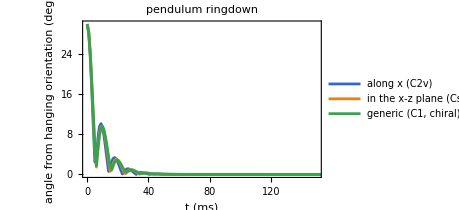
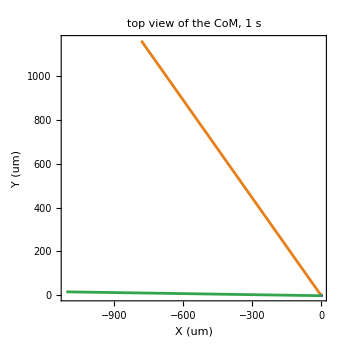

```mathematica
runs=Association[KeyValueMap[Module[{u=#2["u"],q0,tiltAxis},tiltAxis=Normalize[Cross[u,If[Abs[u[[2]]]<0.9,{0,1,0},{1,0,0}]]];q0=qFromTo[RotationMatrix[30Degree,tiltAxis].u,{0,0,1}];#1->simulate[pts[#1],#2["G"],q0,{0,0,0},1.]]&,hang]];
uLab[st_]:=Transpose[quatR[st[[7;;10]]]].{0,0,1};
Module[{ts=Subdivide[0.,1.,1000],cols={RGBColor[0.2,0.4,0.8],RGBColor[0.9,0.5,0.1],RGBColor[0.2,0.65,0.3]}},Column[{Row[{ListLinePlot[KeyValueMap[Function[{key,hs},Transpose[{1000ts,Table[VectorAngle[uLab[runs[key]["state"][t]],hs["u"]]/Degree,{t,ts}]}]],hang],PlotRange->{{0,150},All},Frame->True,FrameLabel->{"t (ms)","angle from hanging orientation (deg)"},PlotLegends->Placed[Keys[hang],Below],PlotStyle->cols,ImageSize->340,PlotLabel->"pendulum ringdown"],ListLinePlot[KeyValueMap[Function[{key,hs},Table[10^6runs[key]["state"][t][[1;;2]],{t,ts}]],hang],AspectRatio->Automatic,Frame->True,FrameLabel->{"X (um)","Y (um)"},PlotStyle->cols,ImageSize->340,PlotLabel->"top view of the CoM, 1 s",PlotRange->All]}],Sequence@@KeyValueMap[Module[{st=runs[#1]["state"][1.],vpred},vpred=quatR[st[[7;;10]]].#2["v_body"];check["run "<>#1,"after 1 s: no spin, orientation = hanging state, velocity = steady prediction",Norm[st[[11;;13]]]<10^-6&&VectorAngle[uLab[st],#2["u"]]<10^-5&&Norm[st[[4;;6]]-vpred]<10^-6Max[Norm[vpred],10^-6],"|omega| = "<>sci[Norm[st[[11;;13]]]]<>" rad/s, horizontal speed "<>num[1000Norm[st[[4;;5]]]]<>" mm/s"]]&,hang]}]]
```

✓ VERIFIED    run along x (C2v):   after 1 s: no spin, orientation = hanging state, velocity = steady prediction
|ω| = 2.05e-14 rad/s, horizontal speed 2.48e-15 mm/s

✓ VERIFIED    run in the x-z plane (Cs):   after 1 s: no spin, orientation = hanging state, velocity = steady prediction
|ω| = 1.75e-12 rad/s, horizontal speed 1.406 mm/s

✓ VERIFIED    run generic (C1, chiral):   after 1 s: no spin, orientation = hanging state, velocity = steady prediction
|ω| = 8.92e-13 rad/s, horizontal speed 1.113 mm/s

The pendulum frequency is set by the stiffness Mg|r_c| and the moment of inertia, as for the graded sphere. The ringdown takes a few tens of milliseconds. Afterwards the chiral particle moves exactly like an achiral one. Its orientation is locked, it has no spin, and its horizontal velocity is constant.

```mathematica
With[{mesh=bodyMesh[Rnum],states=Table[runs["generic (C1, chiral)"]["state"][t],{t,0.,1.,0.005}],rng=10^6runs["generic (C1, chiral)"]["state"][1.][[1;;3]]},Manipulate[Module[{st=states[[k]],x},x=10^6st[[1;;3]];Graphics3D[{drawBody[mesh,x,quatR[st[[7;;10]]],60],If[k>1,{Gray,Thick,Line[10^6states[[1;;k,1;;3]]]},Nothing]},PlotRange->Transpose[{Min[#,0]-120&/@rng,Max[#,0]+120&/@rng}],BoxRatios->Automatic,Lighting->"Neutral",Axes->True,AxesLabel->{"X (um)","Y","Z"},PlotLabel->Row[{"chiral (C1) offset,  t = ",5(k-1)," ms"}],ImageSize->520]],{{k,1,"frame (5 ms steps)"},1,201,1,ControlType->Animator,AnimationRunning->False},SaveDefinitions->True]]
```

## 8. Orbital radius and period

Not applicable, for every offset direction. The steady states have Ω = 0 exactly, so the orbital radius is infinite and there is no orbital period. The table below lists what the particle does instead.

```mathematica
Grid[Prepend[KeyValueMap[{#1,"0","infinite","none",If[#2["vperp"]<10^-9,"hover","straight glide at "<>num[1000#2["vperp"]]<>" mm/s"]}&,hang],{"offset","spin Omega (rad/s)","orbital radius","period","motion"}],Frame->All,Alignment->Left]
```

offset | spin Omega (rad/s) | orbital radius | period | motion
along x (C2v) | 0 | infinite | none | hover
in the x-z plane (Cs) | 0 | infinite | none | straight glide at 1.406 mm/s
generic (C1, chiral) | 0 | infinite | none | straight glide at 1.113 mm/s

## 9. Answer: can an offset direction give chirality?

Geometrically, yes. On a triaxial ellipsoid, any offset that lies neither on a principal axis nor in a principal plane leaves no symmetry element. The particle (surface plus mass) is then chiral, C_1.

Dynamically, no. The gas sees only the surface, which is centrosymmetric, so the gas wrench about H has no polar–axial coupling. About the CoM the thermophoretic torque is the moment of a force through H, T_th = -[r_c]_×f_th. Such a torque can only align the particle, never spin it: T_drag^-1 T_th has eigenvalues {0, ± iμ} for every offset.

What is needed instead. The chirality has to be in the surface, so that the gas forces themselves form a chiral pattern with a moment about the vertical. Shape 3 builds such a surface from spherical harmonics.

## 10. Summary

```mathematica
Column[{Row[{"checks: ",Length[$verifications],"  (",Count[$verifications[[All,3]],"VERIFIED"]," verified)"}],Grid[Prepend[$verifications[[All,1;;3]],Style[#,Bold]&/@{"item","statement","result"}],Frame->All,Alignment->Left,Background->{None,{LightGray}}]}]
```

checks: 19  (19 verified)
item | statement | result
convex | the surface (Shape 1) is convex | VERIFIED
CoM along x (C2v) | CoM = (kappa l/5) diag(a_i^2).d | VERIFIED
CoM in the x-z plane (Cs) | CoM = (kappa l/5) diag(a_i^2).d | VERIFIED
CoM generic (C1, chiral) | CoM = (kappa l/5) diag(a_i^2).d | VERIFIED
shift along x (C2v) | quadrature tensors about the CoM equal the shift of the Shape 1 tensors | VERIFIED
shift in the x-z plane (Cs) | quadrature tensors about the CoM equal the shift of the Shape 1 tensors | VERIFIED
shift generic (C1, chiral) | quadrature tensors about the CoM equal the shift of the Shape 1 tensors | VERIFIED
symbolic | T_th = -[r_c]x f_th through O(eps^2), with r_c = (eps/5)(k_i (1 + 2 eps e_i)) | VERIFIED
spectrum along x (C2v) | eigenvalues of T_drag^-1 T_th are 0 and a complex pair ~ +-i gamma0 |r_c|/c0 | VERIFIED
spectrum in the x-z plane (Cs) | eigenvalues of T_drag^-1 T_th are 0 and a complex pair ~ +-i gamma0 |r_c|/c0 | VERIFIED
spectrum generic (C1, chiral) | eigenvalues of T_drag^-1 T_th are 0 and a complex pair ~ +-i gamma0 |r_c|/c0 | VERIFIED
hang along x (C2v) | stable state: Omega = 0, CoM exactly below H, glide speed matches the first-order formula | VERIFIED
hang in the x-z plane (Cs) | stable state: Omega = 0, CoM exactly below H, glide speed matches the first-order formula | VERIFIED
hang generic (C1, chiral) | stable state: Omega = 0, CoM exactly below H, glide speed matches the first-order formula | VERIFIED
mirror | Cs offset: the glide lies in the mirror plane (y-component zero) | VERIFIED
unstable | each offset also has an inverted state (CoM above H), which is unstable | VERIFIED
run along x (C2v) | after 1 s: no spin, orientation = hanging state, velocity = steady prediction | VERIFIED
run in the x-z plane (Cs) | after 1 s: no spin, orientation = hanging state, velocity = steady prediction | VERIFIED
run generic (C1, chiral) | after 1 s: no spin, orientation = hanging state, velocity = steady prediction | VERIFIED

Shape. Rellipsoid of Shape 1 with density 1 + kappa dhat.r. Defaults: ε = 0.1, e = (1, 0, -1), κ = 0.5 (|r_c| ≈ 2 μm).

Tensors. f_th and f_drag are as in Shape 1. The others are T_th = -[r_c]_×f_th, B = f_drag[r_c]_× and T_drag = T_drag^H + [r_c]_×^ᵀ f_drag[r_c]_×, all exact.

Motion. The particle swings as a damped pendulum into the CoM-below-H orientation. It then hovers (axial offset) or glides in a straight line (in-plane or generic offset).

Orbit. None for any offset: a chiral mass distribution is not enough, and the chirality must be in the surface.